### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Needs["ErrorBarPlots`"];
Off[ListInterpolation::inhr,FindMinimum::lstol,LinkObject::linkw,Kernels::rdead];
```

### Various Constants

```mathematica
(* Planck18 Values *)
obh2pl=0.02237;
obh2plerr=0.00015;
ompl=0.3153;
omplerr=0.0073;
σ8pl=0.8111;
σ8err=0.0060;
h0pl=0.6736;
(* Subscript[H, 0] by Riess et al. https://arxiv.org/abs/1903.07603.pdf *)
h0riess=74/100;
c=299792.458;
```

### Pantheon Data Analysis

#### Import the Data

```mathematica
(* Import the corrected Pantheon data acquired from https://github.com/dscolnic/Pantheon *)
dataPanth=Import[".\\data_Pantheon\\lcparam_full_long_zhel.txt","Table"];
ndatPanth=Length[dataPanth]-1;
```

```mathematica
(* H(α) for ΛCDM *)
H[a_?NumberQ,om_?NumberQ]:=√(om a^-3+(1-om))
(* Luminosity distance Subscript[d, L] *)
dLsol[om_?NumberQ]:=(dLsol[om]=NDSolve[{D[dL[zz]/(1+zz),zz]==c/H[1/(1+zz),om],dL[0]==0},dL,{zz,0,1300},AccuracyGoal->5,PrecisionGoal->5,MaxSteps->Infinity])
(* Hubble free luminosity distance Subscript[D, L] *)
DL[z_?NumberQ,om_?NumberQ]:=1/c(dL[z]/.dLsol[om])[[1]]//Chop
```

```mathematica
Dij0=Import[".\\data_Pantheon\\sys_full_long.txt","List"];
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
```

```mathematica
Covstat=DiagonalMatrix[dataPanth[[All,6]][[2;;-1]]^2];
Covsys=Dij;
Cijtot=Covsys+Covstat;
InvCovTotal=Inverse[Cijtot];
InvCovstat=Inverse[Covstat];
```

```mathematica
(* Full chi^2 with all terms *)
chi2Panth[data_,Mcal_?NumberQ,om_?NumberQ]:=Module[{Δm},
Δm=Table[data[[1+i,5]]-(5 Log10[(1+data[[1+i,3]])/(1+data[[1+i,2]])DL[data[[1+i,2]],om]]+Mcal),{i,1,Length[data]-1}];
Δm.InvCovTotal.Δm]
```

```mathematica
min=FindMinimum[chi2Panth[dataPanth,Mcal,om],{Mcal,23,23.1},{om,0.28,0.29}];
Mcalbf=min[[2,1,2]];
ombf=min[[2,2,2]];
chifun=ListInterpolation[ParallelTable[chi2Panth[dataPanth,Mcal,om],{Mcal,Mcalbf-0.02,Mcalbf+0.02,0.02},{om,ombf-0.02,ombf+0.02,0.02},DistributedContexts->Automatic],{{Mcalbf-0.02,Mcalbf+0.02},{ombf-0.02,ombf+0.02}}];
(* Params that we want to calculate the errors *)
params={Mcal,om};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij=1/2 Table[D[chifun[Mcal,om],params[[p]],params[[d]]]/.min[[2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
errors=Sqrt[Diagonal[cij]];
Print["The best fit parameters for M and Ω_(0  m) are: M=",Mcalbf,"±",errors[[1]]," and Ω_(0  m)=",ombf,"±",errors[[2]]," respectively"]
```

The best fit parameters for M and Ω_(0  m) are: M=23.8086±0.0107297 and Ω_(0  m)=0.299021±0.0218798 respectively

```mathematica
min
```

{1025.63,{Mcal→23.8086,om→0.299021}}

```mathematica
(* The chi^2 subsample of data *)
chi2PanthMsample[M_?NumberQ,om_?NumberQ,range_List,InvCij_List]:=Module[{Δm},
Δm=Table[dataPanth[[1+i,5]]-(5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DL[dataPanth[[1+i,2]],om]]+M),{i,range}];
Δm.InvCij.Δm]
```

```mathematica
(* The chi^2 for radnom data *)
chi2Panthtom[randdatab_,Mcal_?NumberQ,om_?NumberQ,range_,datapos_]:=Module[{residuals,InvCovTotal},
residuals=Table[randdatab[[i,4]]-(5 Log10[(1+randdatab[[i,3]])/(1+randdatab[[i,2]])DL[randdatab[[i,2]],om]]+Mcal),{i,range}];
InvCovTotal=Inverse[(Covsys+Covstat)[[datapos,datapos]]];
residuals.InvCovTotal.residuals]
```

```mathematica
tomall=SortBy[Table[{i,dataPanth[[1+i,2]],dataPanth[[1+i,3]],dataPanth[[1+i,5]],dataPanth[[1+i,6]]},{i,1,ndatPanth}],#[[2]]&];
rangetomall=Table[tomall[[l,1]],{l,1,Length[tomall]}];
invcijall=Inverse[(Covsys+Covstat)[[rangetomall,rangetomall]]];
```

```mathematica
mintot=FindMinimum[chi2PanthMsample[M,om,rangetomall,invcijall],{M,23,23.1},{om,0.29,0.3}]
```

{1025.63,{M→23.8086,om→0.29902}}

## Cross Plot with Systematics

### 1st Bin

```mathematica
tom1=Take[SortBy[Table[{i,dataPanth[[1+i,2]],dataPanth[[1+i,3]],dataPanth[[1+i,5]],dataPanth[[1+i,6]]},{i,1,ndatPanth}],#[[2]]&],262];
rangetom1=Table[tom1[[l,1]],{l,1,Length[tom1]}];
invcijtom1=Inverse[(Covsys+Covstat)[[rangetom1,rangetom1]]];
```

```mathematica
rangetom1
```

{584,586,678,703,729,682,689,589,683,735,727,716,631,701,638,712,576,698,693,697,694,575,626,737,580,721,686,651,742,732,641,688,650,724,574,663,728,578,655,704,718,616,684,591,731,687,739,606,705,679,635,711,672,685,618,722,630,707,621,743,741,612,637,733,646,676,649,581,719,590,598,702,617,645,585,828,609,738,610,577,611,644,661,725,699,708,677,657,600,666,720,636,654,593,583,692,627,662,691,734,619,623,643,652,607,660,754,714,601,639,675,668,700,602,715,648,696,594,723,624,726,592,599,588,667,656,629,653,647,740,355,587,582,736,628,674,681,673,595,573,614,608,659,713,604,462,579,625,824,603,669,680,695,671,706,622,1005,658,613,717,690,665,642,730,709,991,559,597,605,270,710,632,633,572,670,909,640,460,910,265,620,615,634,988,664,969,349,1007,596,456,827,526,281,820,288,787,286,282,415,432,414,530,239,1020,963,802,417,363,244,836,897,520,794,790,749,291,461,775,475,563,788,370,568,993,570,272,755,544,543,459,436,427,522,240,310,892,1001,486,261,466,856,553,397,972,375,249,333,446,882,292,108,250,290,517,237,376,374,571,418,440,539,531}

```mathematica
mintom1=FindMinimum[chi2Panthtom[tom1,Mcal,om,Length[tom1],rangetom1],{Mcal,23,23.1},{om,0.29,0.3}];
Mcalbftom1=mintom1[[2,1,2]];
ombftom1=mintom1[[2,2,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifuntom1=ListInterpolation[ParallelTable[chi2Panthtom[tom1,Mcal,om,Length[tom1],rangetom1],{Mcal,Mcalbftom1-0.02,Mcalbftom1+0.02,0.02},{om,ombftom1-0.02,ombftom1+0.02,0.02},DistributedContexts->Automatic],{{Mcalbftom1-0.02,Mcalbftom1+0.02},{ombftom1-0.02,ombftom1+0.02}}];
paramstom1={Mcal,om};
Fijtom1=1/2Table[D[chifuntom1[Mcal,om],paramstom1[[p]],paramstom1[[d]]]/.mintom1[[2]],{p,1,Length[paramstom1]},{d,1,Length[paramstom1]}];
cijtom1=Inverse[Fijtom1];
errorstom1=√Diagonal[cijtom1];
Print["The best fit parameters of M and Ω_(0  m) for the 1st bin are: M=",Mcalbftom1,"±",errorstom1[[1]]," and Ω_(0  m)=",ombftom1,"±",errorstom1[[2]]," respectively"]
```

The best fit parameters of M and Ω_(0  m) for the 1st bin are: M=23.7805±0.0246335 and Ω_(0  m)=0.0686524±0.170097 respectively

### 2nd Bin

```mathematica
tom2=Take[SortBy[Table[{i,dataPanth[[1+i,2]],dataPanth[[1+i,3]],dataPanth[[1+i,5]],dataPanth[[1+i,6]]},{i,1,ndatPanth}],#[[2]]&],{263,524}];
rangetom2=Table[tom2[[l,1]],{l,1,Length[tom2]}];
invcijtom2=Inverse[(Covsys+Covstat)[[rangetom2,rangetom2]]];
```

```mathematica
rangetom2
```

{304,792,510,317,814,890,536,393,368,413,350,499,401,941,527,467,800,913,242,953,247,801,353,277,303,912,535,558,842,422,301,798,493,300,805,891,847,243,747,364,498,545,389,335,437,339,362,340,477,803,529,341,525,843,506,253,359,248,974,259,784,296,567,551,252,554,569,463,464,819,351,283,465,886,943,772,251,926,516,508,512,307,398,542,387,548,311,347,329,348,830,308,262,320,451,471,942,982,424,295,491,821,822,346,837,951,970,325,532,497,241,345,562,323,458,327,269,344,65,831,550,264,505,287,547,372,983,445,416,409,425,829,523,519,421,337,752,313,513,546,472,373,502,962,555,358,861,919,1013,826,852,294,449,489,501,334,273,408,332,380,776,537,515,396,500,328,931,480,887,390,15,876,318,849,360,488,378,275,450,423,366,377,476,276,779,453,302,915,534,407,549,455,565,280,260,507,88,386,896,305,321,825,855,503,470,496,952,560,875,758,482,756,297,411,799,473,929,431,744,823,902,841,816,468,528,778,388,319,479,284,809,524,361,804,850,862,885,999,986,382,495,854,403,402,478,509,254,893,367,839,312,352,400,889,485,316,209,469,255,314,343,880}

```mathematica
mintom2=FindMinimum[chi2Panthtom[tom2,Mcal,om,Length[tom2],rangetom2],{Mcal,23,23.1},{om,0.29,0.3}];
Mcalbftom2=mintom2[[2,1,2]];
ombftom2=mintom2[[2,2,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifuntom2=ListInterpolation[ParallelTable[chi2Panthtom[tom2,Mcal,om,Length[tom2],rangetom2],{Mcal,Mcalbftom2-0.02,Mcalbftom2+0.02,0.02},{om,ombftom2-0.02,ombftom2+0.02,0.02},DistributedContexts->Automatic],{{Mcalbftom2-0.02,Mcalbftom2+0.02},{ombftom2-0.02,ombftom2+0.02}}];
paramstom2={Mcal,om};
Fijtom2=1/2Table[D[chifuntom2[Mcal,om],paramstom2[[p]],paramstom2[[d]]]/.mintom2[[2]],{p,1,Length[paramstom2]},{d,1,Length[paramstom2]}];
cijtom2=Inverse[Fijtom2];
errorstom2=√Diagonal[cijtom2];
Print["The best fit parameters of M and Ω_(0  m) for the 2nd bin are: M=",Mcalbftom2,"±",errorstom2[[1]]," and Ω_(0  m)=",ombftom2,"±",errorstom2[[2]]," respectively"]
```

The best fit parameters of M and Ω_(0  m) for the 2nd bin are: M=23.8902±0.055004 and Ω_(0  m)=0.562049±0.195871 respectively

### 3rd Bin

```mathematica
tom3=Take[SortBy[Table[{i,dataPanth[[1+i,2]],dataPanth[[1+i,3]],dataPanth[[1+i,5]],dataPanth[[1+i,6]]},{i,1,ndatPanth}],#[[2]]&],{525,786}];
rangetom3=Table[tom3[[l,1]],{l,1,Length[tom3]}];
invcijtom3=Inverse[(Covsys+Covstat)[[rangetom3,rangetom3]]];
```

```mathematica
mintom3=FindMinimum[chi2Panthtom[tom3,Mcal,om,Length[tom3],rangetom3],{Mcal,23,23.1},{om,0.29,0.3}];
Mcalbftom3=mintom3[[2,1,2]];
ombftom3=mintom3[[2,2,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifuntom3=ListInterpolation[ParallelTable[chi2Panthtom[tom3,Mcal,om,Length[tom3],rangetom3],{Mcal,Mcalbftom3-0.02,Mcalbftom3+0.02,0.02},{om,ombftom3-0.02,ombftom3+0.02,0.02},DistributedContexts->Automatic],{{Mcalbftom3-0.02,Mcalbftom3+0.02},{ombftom3-0.02,ombftom3+0.02}}];
paramstom3={Mcal,om};
Fijtom3=1/2Table[D[chifuntom3[Mcal,om],paramstom3[[p]],paramstom3[[d]]]/.mintom3[[2]],{p,1,Length[paramstom3]},{d,1,Length[paramstom3]}];
cijtom3=Inverse[Fijtom3];
errorstom3=√Diagonal[cijtom3];
Print["The best fit parameters of M and Ω_(0  m) for the 2nd bin are: M=",Mcalbftom3,"±",errorstom3[[1]]," and Ω_(0  m)=",ombftom3,"±",errorstom3[[2]]," respectively"]
```

The best fit parameters of M and Ω_(0  m) for the 2nd bin are: M=23.748±0.0611502 and Ω_(0  m)=0.183283±0.110586 respectively

### 4th Bin

```mathematica
tom4=Take[SortBy[Table[{i,dataPanth[[1+i,2]],dataPanth[[1+i,3]],dataPanth[[1+i,5]],dataPanth[[1+i,6]]},{i,1,ndatPanth}],#[[2]]&],{787,ndatPanth}];
rangetom4=Table[tom4[[l,1]],{l,1,Length[tom4]}];
invcijtom4=Inverse[(Covsys+Covstat)[[rangetom4,rangetom4]]];
```

```mathematica
rangetom4
```

{992,796,921,903,780,68,981,914,769,142,118,748,767,1011,760,998,227,109,759,123,908,1021,147,783,38,1022,1000,125,207,751,9,53,92,153,171,966,184,964,946,182,80,1012,924,62,2,93,105,959,899,863,1,806,94,770,939,920,71,151,140,170,196,948,229,846,30,762,222,106,218,189,211,1002,46,904,116,39,224,176,17,181,56,175,70,763,114,923,131,58,203,81,120,19,101,137,143,61,95,138,14,33,90,217,130,191,36,45,174,895,34,145,129,165,937,186,173,126,141,210,72,152,195,89,205,144,83,208,3,66,110,50,63,113,11,167,233,69,96,214,31,192,26,49,199,202,132,115,102,111,226,234,148,190,23,1034,187,177,85,1042,149,155,32,84,52,40,162,194,91,97,179,24,200,133,168,139,212,136,98,13,20,5,198,82,197,104,100,164,44,159,160,107,41,57,27,103,221,225,55,117,135,87,216,1038,16,60,180,169,59,4,76,163,79,185,12,201,156,21,67,183,77,128,172,223,51,166,1045,206,10,22,42,54,161,204,1041,1040,193,158,25,18,235,35,1046,1033,47,230,1048,1035,1023,1036,1037,1031,1044,1047,1024,1032,1039,1043,1025,1026,1027,1028,1030,1029}

```mathematica
mintom4=FindMinimum[chi2Panthtom[tom4,Mcal,om,Length[tom4],rangetom4],{Mcal,23,23.1},{om,0.29,0.3}];
Mcalbftom4=mintom4[[2,1,2]];
ombftom4=mintom4[[2,2,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifuntom4=ListInterpolation[ParallelTable[chi2Panthtom[tom4,Mcal,om,Length[tom4],rangetom4],{Mcal,Mcalbftom4-0.02,Mcalbftom4+0.02,0.02},{om,ombftom4-0.02,ombftom4+0.02,0.02},DistributedContexts->Automatic],{{Mcalbftom4-0.02,Mcalbftom4+0.02},{ombftom4-0.02,ombftom4+0.02}}];
paramstom4={Mcal,om};
Fijtom4=1/2Table[D[chifuntom4[Mcal,om],paramstom4[[p]],paramstom4[[d]]]/.mintom4[[2]],{p,1,Length[paramstom4]},{d,1,Length[paramstom4]}];
cijtom4=Inverse[Fijtom4];
errorstom4=√Diagonal[cijtom4];
Print["The best fit parameters of M and Ω_(0  m) for the 2nd bin are: M=",Mcalbftom4,"±",errorstom4[[1]]," and Ω_(0  m)=",ombftom4,"±",errorstom4[[2]]," respectively"]
```

The best fit parameters of M and Ω_(0  m) for the 2nd bin are: M=23.8467±0.0551831 and Ω_(0  m)=0.330781±0.0630128 respectively

### Cross Plot

```mathematica
(* Best Fits of ℳ for the four bins *)
listMcal={{{Mean[tom1[[All,2]]],Mcalbftom1},ErrorBar[{tom1[[1,2]]-Mean[tom1[[All,2]]],tom1[[262,2]]-Mean[tom1[[All,2]]]},errorstom1[[1]]]},{{Mean[tom2[[All,2]]],Mcalbftom2},ErrorBar[{tom2[[1,2]]-Mean[tom2[[All,2]]],tom2[[262,2]]-Mean[tom2[[All,2]]]},errorstom2[[1]]]},{{Mean[tom3[[All,2]]],Mcalbftom3},ErrorBar[{tom3[[1,2]]-Mean[tom3[[All,2]]],tom3[[262,2]]-Mean[tom3[[All,2]]]},errorstom3[[1]]]},{{Mean[tom4[[All,2]]],Mcalbftom4},ErrorBar[{tom4[[1,2]]-Mean[tom4[[All,2]]],tom4[[262,2]]-Mean[tom4[[All,2]]]},errorstom4[[1]]]}};
(* ℳ Plot *)
Mcalplotcross=ErrorListPlot[listMcal,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],Frame->True,PlotRange->{{-0.02,2.35},{23.65,23.97}},PlotStyle->Blue,ImageSize->700,FrameLabel->{"z","ℳ"},FrameStyle->Directive[Black,Thick],Epilog->{Text["1st Bin",{0.11,23.74}],Text["2nd Bin",{0.2,23.955}],Text["3rd Bin",{0.32,23.67}],Text["4th Bin",{0.75,23.91}],,{Dashing[0.02],Line[{{0,Mcalbf},{8,Mcalbf}}]},{Dashing[0.008],Line[{{0,Mcalbf+errors[[1]]},{8,Mcalbf+errors[[1]]}}]},{Dashing[0.008],Line[{{0,Mcalbf-errors[[1]]},{8,Mcalbf-errors[[1]]}}]}}];
```

```mathematica
(* Best Fit of Subscript[Ω, 0m] for the four bins *)
listom={{{Mean[tom1[[All,2]]],ombftom1},ErrorBar[{tom1[[1,2]]-Mean[tom1[[All,2]]],tom1[[262,2]]-Mean[tom1[[All,2]]]},errorstom1[[2]]]},{{Mean[tom2[[All,2]]],ombftom2},ErrorBar[{tom2[[1,2]]-Mean[tom2[[All,2]]],tom2[[262,2]]-Mean[tom2[[All,2]]]},errorstom2[[2]]]},{{Mean[tom3[[All,2]]],ombftom3},ErrorBar[{tom3[[1,2]]-Mean[tom3[[All,2]]],tom3[[262,2]]-Mean[tom3[[All,2]]]},errorstom3[[2]]]},{{Mean[tom4[[All,2]]],ombftom4},ErrorBar[{tom4[[1,2]]-Mean[tom4[[All,2]]],tom4[[262,2]]-Mean[tom4[[All,2]]]},errorstom4[[2]]]}};
(* Subscript[Ω, 0m] Plot *)
omplotcross=ErrorListPlot[listom,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],Frame->True,PlotRange->{{-0.02,2.35},{-0.25,0.85}},PlotStyle->Blue,ImageSize->700,FrameLabel->{"z","Ω_(0  m)"},FrameStyle->Directive[Black,Thick],Axes->False,Epilog->{Text["1st Bin",{0.12,-0.16}],Text["2nd Bin",{0.2,0.79}],Text["3rd Bin",{0.325,0.04}],Text["4th Bin",{0.75,0.42}],,{Dashing[0.02],Line[{{0,ombf},{8,ombf}}]},{Dashing[0.008],Line[{{0,ombf+errors[[2]]},{8,ombf+errors[[2]]}}]},{Dashing[0.008],Line[{{0,ombf-errors[[2]]},{8,ombf-errors[[2]]}}]}}];
```

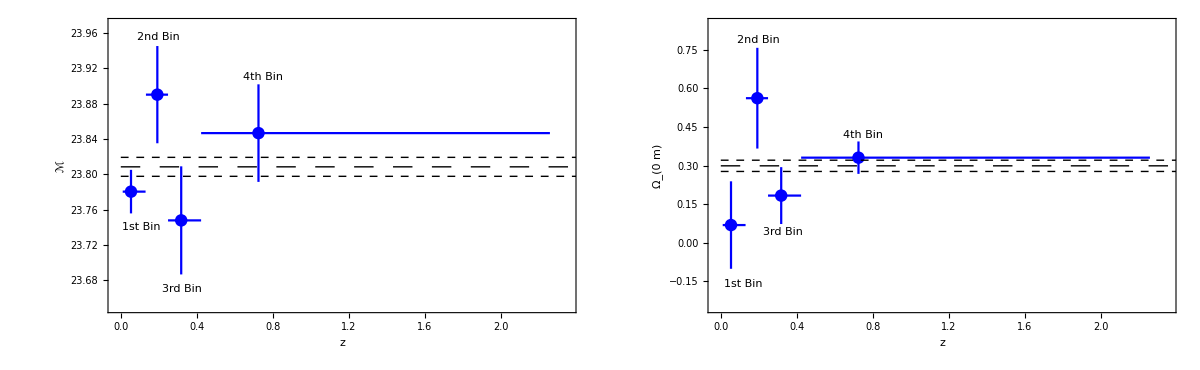

```mathematica
crossplot2=GraphicsGrid[{{Mcalplotcross,omplotcross}},Spacings->0,ImageSize->1200]
```

```mathematica
Export[NotebookDirectory[]<>"crossplot_2.pdf",crossplot2,ImageResolution->1000];
```